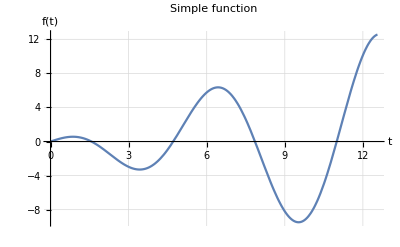

```mathematica
Plot[t*Cos[t], {t, 0, 4*3.14},
PlotLabel-> "Simple function",
GridLines-> Automatic,
AxesLabel-> {"t", "f(t)"}]
```

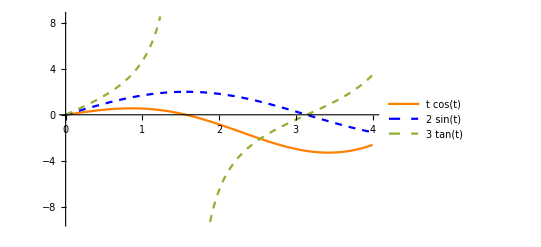

```mathematica
Plot[{t*Cos[t], 2*Sin[t], 3*Tan[t]}, {t, 0, 4},
PlotStyle->{Orange, {Blue,Dashed}, Dashed}, 
PlotLegends->"Expressions"]
```

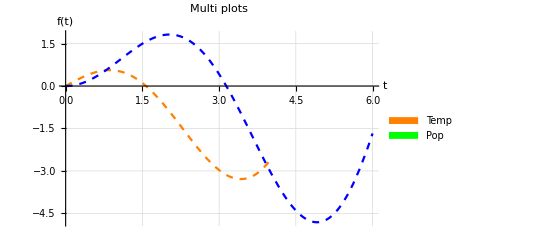

```mathematica
plot1 = Plot[{t*Cos[t]}, {t, 0, 4},
PlotStyle->{Orange, Dashed}];
plot2 = Plot[{t*Sin[t]}, {t, 0, 6},
PlotStyle->{Blue, Dashed}];

Legended [
Show[plot1, plot2, 
PlotLabel-> "Multi plots",
AxesLabel->{"t", "f(t)"},
GridLines->Automatic,
PlotRange->All],

SwatchLegend[{Orange, Green}, {"Temp","Pop"}]
]
```

```mathematica
pt1 = {{1,2}, {2, 3}, {3, -1}}

pta = ListPlot[pt1,
GridLines->Automatic,
PlotStyle->{Green, PointSize[0.06]}
];
```

{{1,2},{2,3},{3,-1}}

```mathematica
ptb = ListLinePlot[pt1,
GridLines->Automatic
];
```

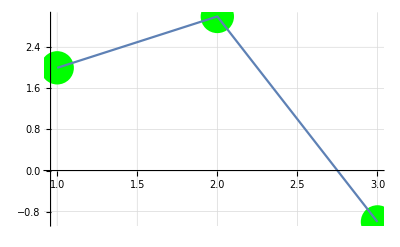

```mathematica
Show[pta, ptb]
```

```mathematica
data1 = Table[{t, 2Cos[t]+RandomReal[]-0.5}, {t, 0, 4π, 2π/100}];
```

```mathematica
data2=Table[{t,2 Cos[t]+RandomReal[]-0.5},{t,0, 4 π, 2π/100}]
```

{{0,2.4936},{π/50,1.87651},{π/25,2.22437},{(3 π)/50,1.88989},{(2 π)/25,1.5444},{π/10,2.28543},{(3 π)/25,1.58607},{(7 π)/50,2.23147},{(4 π)/25,2.13468},{(9 π)/50,2.16163},{π/5,1.59297},{(11 π)/50,1.5498},{(6 π)/25,1.18274},{(13 π)/50,1.10559},{(7 π)/25,1.12945},{(3 π)/10,0.968559},{(8 π)/25,1.41862},{(17 π)/50,1.25435},{(9 π)/25,0.915395},{(19 π)/50,0.334586},{(2 π)/5,0.503382},{(21 π)/50,0.702625},{(11 π)/25,0.451547},{(23 π)/50,-0.18648},{(12 π)/25,0.472098},{π/2,-0.320093},{(13 π)/25,-0.374291},{(27 π)/50,-0.488301},{(14 π)/25,-0.515142},{(29 π)/50,-0.827987},{(3 π)/5,-0.327801},{(31 π)/50,-0.790702},{(16 π)/25,-0.887902},{(33 π)/50,-0.670686},{(17 π)/25,-1.36912},{(7 π)/10,-0.847971},{(18 π)/25,-0.948524},{(37 π)/50,-1.80499},{(19 π)/25,-1.83637},{(39 π)/50,-1.7221},{(4 π)/5,-1.52225},{(41 π)/50,-1.20665},{(21 π)/25,-2.04536},{(43 π)/50,-1.37814},{(22 π)/25,-2.0664},{(9 π)/10,-1.77537},{(23 π)/25,-1.96345},{(47 π)/50,-1.95124},{(24 π)/25,-1.68979},{(49 π)/50,-2.0223},{π,-1.65417},{(51 π)/50,-1.97731},{(26 π)/25,-2.21447},{(53 π)/50,-2.45887},{(27 π)/25,-2.42608},{(11 π)/10,-2.37511},{(28 π)/25,-2.08842},{(57 π)/50,-1.46384},{(29 π)/25,-1.28514},{(59 π)/50,-1.9223},{(6 π)/5,-1.36191},{(61 π)/50,-1.20369},{(31 π)/25,-1.24143},{(63 π)/50,-1.75056},{(32 π)/25,-1.14843},{(13 π)/10,-1.37217},{(33 π)/25,-0.915499},{(67 π)/50,-1.0052},{(34 π)/25,-0.883071},{(69 π)/50,-0.277276},{(7 π)/5,-0.179568},{(71 π)/50,-0.0307095},{(36 π)/25,0.113339},{(73 π)/50,-0.563165},{(37 π)/25,-0.149802},{(3 π)/2,0.105499},{(38 π)/25,0.232978},{(77 π)/50,0.402737},{(39 π)/25,0.797411},{(79 π)/50,0.193623},{(8 π)/5,0.885678},{(81 π)/50,0.43817},{(41 π)/25,1.15204},{(83 π)/50,0.637287},{(42 π)/25,0.795804},{(17 π)/10,0.727681},{(43 π)/25,1.54685},{(87 π)/50,1.32387},{(44 π)/25,1.58772},{(89 π)/50,1.39655},{(9 π)/5,2.11618},{(91 π)/50,1.81537},{(46 π)/25,2.12974},{(93 π)/50,1.31904},{(47 π)/25,1.99305},{(19 π)/10,1.95307},{(48 π)/25,1.83778},{(97 π)/50,1.53887},{(49 π)/25,1.67924},{(99 π)/50,2.0736},{2 π,2.09104},{(101 π)/50,2.39872},{(51 π)/25,2.23079},{(103 π)/50,1.73343},{(52 π)/25,1.91889},{(21 π)/10,1.85066},{(53 π)/25,2.09952},{(107 π)/50,2.11396},{(54 π)/25,1.61747},{(109 π)/50,1.71111},{(11 π)/5,1.85673},{(111 π)/50,1.32534},{(56 π)/25,1.84777},{(113 π)/50,1.05746},{(57 π)/25,1.06786},{(23 π)/10,1.26946},{(58 π)/25,0.788798},{(117 π)/50,1.13271},{(59 π)/25,0.634264},{(119 π)/50,0.554207},{(12 π)/5,0.855855},{(121 π)/50,0.474027},{(61 π)/25,0.12584},{(123 π)/50,-0.0121528},{(62 π)/25,0.265982},{(5 π)/2,-0.498492},{(63 π)/25,-0.469074},{(127 π)/50,-0.165751},{(64 π)/25,-0.588969},{(129 π)/50,-0.304875},{(13 π)/5,-0.370561},{(131 π)/50,-0.682019},{(66 π)/25,-1.11562},{(133 π)/50,-0.878481},{(67 π)/25,-0.632989},{(27 π)/10,-1.09772},{(68 π)/25,-1.0673},{(137 π)/50,-1.45767},{(69 π)/25,-1.93051},{(139 π)/50,-1.16165},{(14 π)/5,-1.70952},{(141 π)/50,-1.39536},{(71 π)/25,-2.20492},{(143 π)/50,-2.09851},{(72 π)/25,-1.73484},{(29 π)/10,-1.89137},{(73 π)/25,-1.73335},{(147 π)/50,-1.66147},{(74 π)/25,-2.10717},{(149 π)/50,-1.559},{3 π,-2.14772},{(151 π)/50,-1.70385},{(76 π)/25,-2.02354},{(153 π)/50,-2.15288},{(77 π)/25,-1.64298},{(31 π)/10,-1.88365},{(78 π)/25,-1.99789},{(157 π)/50,-1.34064},{(79 π)/25,-1.98018},{(159 π)/50,-2.14459},{(16 π)/5,-1.98721},{(161 π)/50,-1.66092},{(81 π)/25,-1.95099},{(163 π)/50,-1.0713},{(82 π)/25,-1.52292},{(33 π)/10,-0.87121},{(83 π)/25,-1.35651},{(167 π)/50,-0.874128},{(84 π)/25,-0.638105},{(169 π)/50,-0.577037},{(17 π)/5,-0.674964},{(171 π)/50,-0.0963784},{(86 π)/25,-0.0414035},{(173 π)/50,-0.369641},{(87 π)/25,0.0607501},{(7 π)/2,-0.0675991},{(88 π)/25,0.396803},{(177 π)/50,0.709978},{(89 π)/25,0.769959},{(179 π)/50,0.136402},{(18 π)/5,0.527486},{(181 π)/50,0.33761},{(91 π)/25,0.66447},{(183 π)/50,0.61481},{(92 π)/25,0.606818},{(37 π)/10,0.837522},{(93 π)/25,1.65626},{(187 π)/50,1.28724},{(94 π)/25,1.03677},{(189 π)/50,1.71572},{(19 π)/5,1.3682},{(191 π)/50,1.22839},{(96 π)/25,1.40694},{(193 π)/50,1.76746},{(97 π)/25,1.43717},{(39 π)/10,1.48161},{(98 π)/25,1.82644},{(197 π)/50,1.86313},{(99 π)/25,1.8347},{(199 π)/50,1.76456},{4 π,2.3259}}

```mathematica
data2;
```

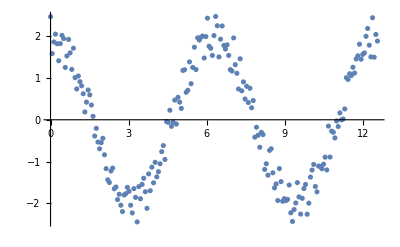

```mathematica
dataPlot = ListPlot[data1]
```